## The electron pass through the single(multi) barrier (barriers). Transfer Matrix Technique

Let's consider the electron transition through the tunneling barrier in the tunnel junction
 (see potential profile Fig.1).  Consider the both cases E_1 < U_b and E_1 > U_b .

Fig.1 potential profile of the rectangular barrier. 
The tunneling case is shown for E_1<U_b, number of interfaces is 2.

#### General knowledge about tunneling and Transfer Matrix Technique

The motions states of the tunneling electrons (E) can be found from the solution of the homogeneous Shrödinger equation (1):

-ℏ^2/(2m)d^2/dx^2 Ψ+(U(x)-E)Ψ=0,                                                       (1)
or 
(d^2 Ψ(x))/dx^2-(2m)/ℏ^2(U(x)-E)Ψ(x)=0,

where U (x)  have to be constant in some region or piecewise continuous function. For E-energies, corresponding to the tunneling. 
For example:  (d^2 Ψ_1(x))/dx^2-(2 m_1)/ℏ^2(-E_1)Ψ_1(x)=0, (for left side of the junction);  or (d^2 Ψ_1(x))/dx^2+(2 m_1)/ℏ^2(+E_1)Ψ_1(x)=0
                         (d^2 Ψ_2(x))/dx^2-(2 m_2)/ℏ^2(U_b-E_1)Ψ_2(x)=0 (for the barrier);  or  (d^2 Ψ_2(x))/dx^2+(2 m_2)/ℏ^2(E_1-U_b)Ψ_2(x)=0
                          (d^2 Ψ_3(x))/dx^2-(2 m_3)/ℏ^2(U_3-E_1)Ψ_3(x)=0 (for the right-side);  or  (d^2 Ψ_3(x))/dx^2+(2 m_3)/ℏ^2(E_1-U_3)Ψ_3(x)=0
                          
(2 m_r)/ℏ^2=c_r - dimensional coefficient,  or like this: (2 m_r*m_0)/(ℏ^2 m_0)=c_0M_eff , where c_0= 0.2624 1/[(eV)*(Å^2)] and M_eff=m_r/m_0 ,  m_0 is free electron mass. 
    The solution (1) in the regions 1 and 3 can be presented as follows:

Ψ_r(x)=A_r exp( I k_r x)+B_r exp(-I k_r x) ,                               (2)
I is imaginary unit, r - is index of the region (For the single barrier model: r =1,2 and 3)
in common case r= 1,2,3,..,N
Applying the boundary conditions (BCs) :  
1/m_i∂_x Ψ_i(x_i)= 1/(m_(i+1))∂_x Ψ_(i+1)(x_i) , and  also
Ψ_i(x_i)= Ψ_(i+1)(x_i) , 
where  i=1 ,2,.. , n , where n is the mount of interfaces, n=N-1 and thus N=n+1.  
The coordinate of interfaces is determined as x=x_i
BCs give  2n  number of equations,
the matrix form of this equations  is :
Take i =1  for the first interface (x=x_1) ,we have:
(a_1 | a_2
a_3 | a_4)(A_i
B_i)= (a_5 | a_6
a_7 | a_8)(A_(i+1)
B_(i+1))   → (a_1 | a_2
a_3 | a_4)(A_1
B_1)= (a_5 | a_6
a_7 | a_8)(A_2
B_2)   
Take i =2  for the second interface (x=x_2) and have: 
 (a_9 | a_10
a_11 | a_12)(A_i
B_i)= (a_13 | a_14
a_15 | a_16)(A_(i+1)
B_(i+1)) →  (a_9 | a_10
a_11 | a_12)(A_2
B_2)= (a_13 | a_14
a_15 | a_16)(A_3
B_3) 
where the coefficients a_1.. a_8 contain x_1 ( x_1 = 0 if you make  the origin of x-axis in this point); a_9.. a_16 contain x_2
Or it can be represented in the following matrix form in general case
Q_j(A_i
B_i)=Q_(j+1)(A_(i+1)
B_(i+1))   ↔(a_p | a_(p+1)
a_(p+2) | a_(p+3))(A_i
B_i)=(a_(p+4) | a_(p+5)
a_(p+6) | a_(p+7))(A_(i+1)
B_(i+1))   
for n=2 and N=3  it gives j=1 and j=3; 
In common case the maximal j  = (2n-1) , and it is odd numbers j=1, 3, 5, .. (2n-1).
 and total amount of the matrixes is the same as  the number of equations,which is 2n  and we have the set {Q_1,Q_2, .. , Q_(2n)} 
p is index which numerate the matrix elements: when i=1  then p=1, when i=3 index p becomes p=9 or in common case p=8i-7
As a result, the relation between amplitudes in region r=1 and r=3 is   (A_1
B_1)=Inverse[Q_1]Q_2 Inverse[Q_3]Q_4(A_3
B_3);
In common case: it will be:  (A_1
B_1)=Inverse[Q_1]×Q_2×.. Inverse[Q_x]×Q_(x+1)..×Inverse[Q_(2n-1)]×Q_(2n)(A_N
B_N)
Remind that r,i,j ,x  are indexes
So, our interest is element g_11= G_[[1,1]] of the matrix, keeping in mind that set {a_1,a_2, a_3.. a_(8n)} is found.
G=Inverse[Q_1]×Q_2×.. Inverse[Q_x]×Q_(x+1)..×Inverse[Q_(2n-1)]×Q_(2n)
and  
(A_1
B_1)=G (A_N
B_N) ,
  G[[1,1]] element is the result for us, because it connects  A_1 with A_N
Transmission=m_1/m_N k_N/k_1*(|A_N|^2)/(|A_1|^2)
TransmissionForSimpleBarrier=m1/m3*k3/k1*1/(G[[1,1]] *Conjugate[G[[1,1]] ),
where m1=m_1 and m3= m_3 are effective electron mass, k_1 is Fermi wave number for r=1, k_3 is Fermi wave number for r=3.

### Program-Example of Transfer Matrix tech: finding the Transmission as a function of energy E for rectangle barrier:

```mathematica
ClearAll;
Subscript[a, 1]=k1[E1,m1]/m1*Exp[I*k1[E1,m1]*x1];
Subscript[a, 2]=-k1[E1,m1]/m1*Exp[-I*k1[E1,m1]*x1];
Subscript[a, 5]=k2[E1,Ub,m2]/m2*Exp[I*k2[E1,Ub,m2]*x1];
Subscript[a, 6]=-k2[E1,Ub,m2]/m2*Exp[-I*k2[E1,Ub,m2]*x1];

Subscript[a, 3]=Exp[I*k1[E1,m1]*x1];
Subscript[a, 4]=Exp[-I*k1[E1,m1]*x1];
Subscript[a, 7]=Exp[I*k2[E1,Ub,m2]*x1];
Subscript[a, 8]=Exp[-I*k2[E1,Ub,m2]*x1];

Subscript[a, 9]=k2[E1,Ub,m2]/m2*Exp[I*k2[E1,Ub,m2]*x2];
Subscript[a, 10]=-k2[E1,Ub,m2]/m2*Exp[-I*k2[E1,Ub,m2]*x2];
Subscript[a, 13]=k3[E1,V,m3]/m3*Exp[I*k3[E1,V,m3]*x2];
Subscript[a, 14]=-k3[E1,V,m3]/m3*Exp[-I*k3[E1,V,m3]*x2];

Subscript[a, 11]=Exp[I*k2[E1,Ub,m2]*x2];
Subscript[a, 12]=Exp[-I*k2[E1,Ub,m2]*x2];
Subscript[a, 15]=Exp[I*k3[E1,V,m3]*x2];
Subscript[a, 16]=Exp[-I*k3[E1,V,m3]*x2];

 
(*Now build the Matrixes: *)

Ma1=({{Subscript[a, 1], Subscript[a, 2]}, {Subscript[a, 3], Subscript[a, 4]}});
Ma2=({{Subscript[a, 5], Subscript[a, 6]}, {Subscript[a, 7], Subscript[a, 8]}});
Ma3=({{Subscript[a, 9], Subscript[a, 10]}, {Subscript[a, 11], Subscript[a, 12]}});
Ma4=({{Subscript[a, 13], Subscript[a, 14]}, {Subscript[a, 15], Subscript[a, 16]}});

Q1=FullSimplify[Inverse[Ma1].Ma2.Inverse[Ma3].Ma4];
(* NOTE! the following way as use Q1 =FullSimplify[(1/Qa1).Qa2.(1/Qa3).Qa4] is WRONG, becasue 1/Qa1 is not inversed matrix *)
(* Inverse[Qa1]={{a6/(-a2 a5+a1 a6),-a2/(-a2 a5+a1 a6)},{-a5/(-a2 a5+a1 a6),a1/(-a2 a5+a1 a6)}} while 1/Qa1={{1/a1,1/a2},{1/a5,1/a6}}  *)
FullSimplify[Q1[[1,1]]]
```

1/(4 m2 m3 k1[E1,m1] k2[E1,Ub,m2])ⅇ^(-ⅈ (x1 k1[E1,m1]+(x1+x2) k2[E1,Ub,m2]-x2 k3[E1,V,m3])) (-ⅇ^(2 ⅈ x2 k2[E1,Ub,m2]) (m2 k1[E1,m1]-m1 k2[E1,Ub,m2]) (-m3 k2[E1,Ub,m2]+m2 k3[E1,V,m3])+ⅇ^(2 ⅈ x1 k2[E1,Ub,m2]) (m2 k1[E1,m1]+m1 k2[E1,Ub,m2]) (m3 k2[E1,Ub,m2]+m2 k3[E1,V,m3]))

```mathematica
(*NOW COPY AND PAST THIS Q1[[1,1]] ON THE RIGHT SIDE as making the "USER-FUNCTION" M11[E1_,x1_,x2_,Ub_,V_,m1_,m2_,m3_] :*)

Q11[E1_,x1_,x2_,Ub_,V_,m1_,m2_,m3_]:=1/(4 m2 m3 k1[E1,m1] k2[E1,Ub,m2])ⅇ^(-ⅈ (x1 k1[E1,m1]+(x1+x2) k2[E1,Ub,m2]-x2 k3[E1,V,m3])) (-ⅇ^(2 ⅈ x2 k2[E1,Ub,m2]) (m2 k1[E1,m1]-m1 k2[E1,Ub,m2]) (-m3 k2[E1,Ub,m2]+m2 k3[E1,V,m3])+ⅇ^(2 ⅈ x1 k2[E1,Ub,m2]) (m2 k1[E1,m1]+m1 k2[E1,Ub,m2]) (m3 k2[E1,Ub,m2]+m2 k3[E1,V,m3]));

(* Transmission with effective masses *)

c=0.262468;       (* 1/(eV*Angstrom^2) *)
(*   
c=(2*Subscript[m, 0]*eV)/(h*h/4 π^2)*10^-20 =  0.262468 per 1 eV  (* 1/Angstrom^2 *)
*)
(*  m = Subscript[m, 0] - free electon mass, h - Dirac const. *)

m0=1.0;
(*m1=0.8*m0;
m2=1.8*m0;
m3=0.8*m0; *)

L=10.0 (*units = Angstroms*);
Va=0.0 (*units = eV*);
UB=3.8 (*units = eV*);

k1[E1_,m1_]:= (c*E1*(m1/m0))^(1/2);     (*1/Angstrom*) 
k2[E1_,Ub_,m2_]:=(c*(E1-Ub)*(m2/m0))^(1/2);          (*1/Angstrom*)     
k3[E1_,V_,m3_]:=(c*(E1+V)*(m3/m0))^(1/2);     

Dtransmission[E1_,m1_,m2_,m3_]:=Re[m1/m3*k3[E1,Va,m3]/k1[E1,m1]*1/(Q11[E1,0,L,UB,Va,m1,m2,m3]*Conjugate[Q11[E1,0,L,UB,Va,m1,m2,m3]])]
```

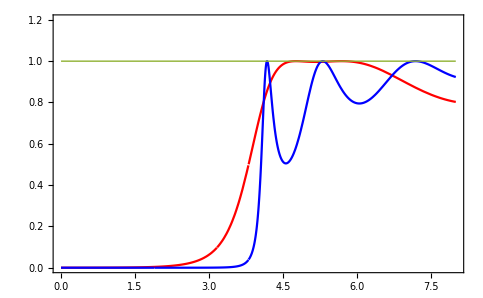

```mathematica
m1=0.99*m0;    m12=1.0*m0;
m2=0.2*m0;    m22=1.0*m0;
m3=0.99*m0;    m32=1.0*m0;
Plot[{Dtransmission[E1,m1,m2,m3],Dtransmission[E1,m12,m22,m32],1},{E1,0,8}, PlotRange->{{0,8.0},{0,1.2}}, Frame-> True, PlotStyle->{Red, Blue, Thin}]
(*RESULT*)
```